```mathematica
f1[x1_,x2_]=x1*r1*((x1-c1)/(x1+c1)*(1-x1/k1))-a*x1*x2
f2[x1_,x2_]=x2*r2*((x2-c2)/(x2+c2)*(1-x2/k2))-a*x1*x2
```

(0.05 (1-x1/150000) (-3000+x1) x1)/(3000+x1)-(x1 x2)/100000000

-(x1 x2)/100000000+(0.08 (1-x2/400000) (-15000+x2) x2)/(15000+x2)

```mathematica
r1=0.05;
r2=0.08;
k1=150000;
k2=400000;
a=10^-8;
c1=3000;
c2=15000;
```

```mathematica
Solve[{f1[x1,x2]==0,f2[x1,x2]==0, x1≠ 0, x2≠0},{x1,x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→3018.44+0. ⅈ,x2→15011.8+0. ⅈ},{x1→3535.18+0. ⅈ,x2→399809.+0. ⅈ},{x1→137698.+0. ⅈ,x2→392568.+0. ⅈ},{x1→149513.+0. ⅈ,x2→15595.+0. ⅈ}}

```mathematica
Solve[{f1[x1,x2]/x1==0,f2[x1,x2]/x2==0, x1≠ 0, x2≠0},{x1,x2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→3018.44+0. ⅈ,x2→15011.8+0. ⅈ},{x1→3535.18+0. ⅈ,x2→399809.+0. ⅈ},{x1→137698.+0. ⅈ,x2→392568.+0. ⅈ},{x1→149513.+0. ⅈ,x2→15595.+0. ⅈ}}

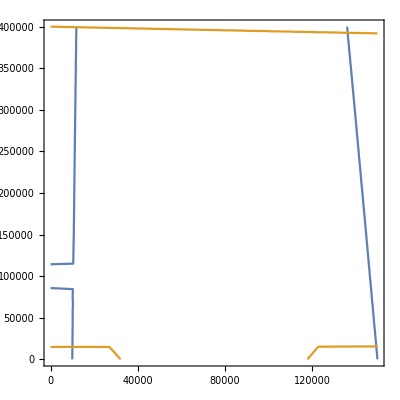

```mathematica
ContourPlot[{f1[x1,x2]==0,f2[x1,x2]==0},{x1,0,150000},{x2,0,400000}]
```

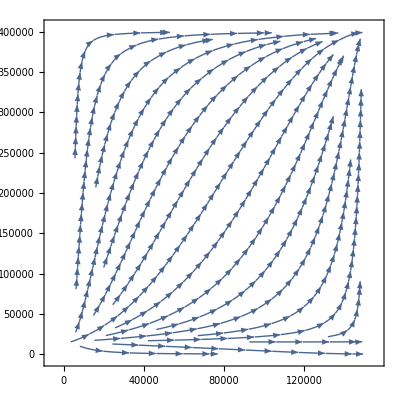

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,150000},{x2,0,400000}]
```

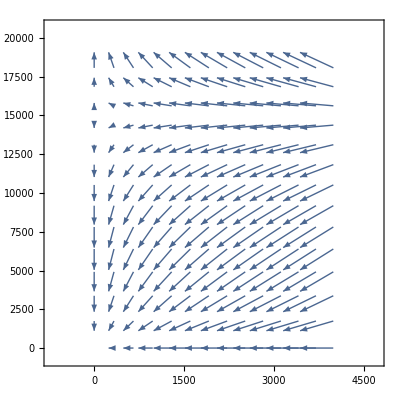

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,4000},{x2,0,20000}]
(*Near (x1,x2)=(3000,15000)*)
```

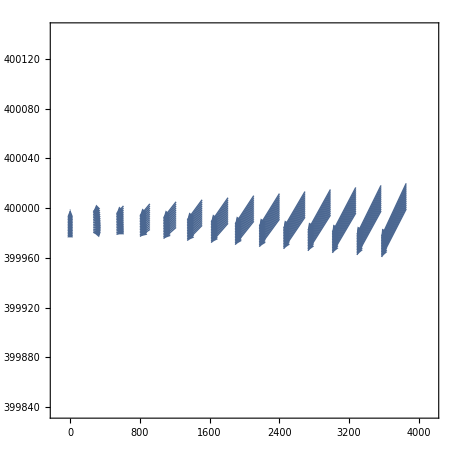

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,4000},{x2,399980,400000}]
(*Near (x1,x2)=(3000,400000)*)
```

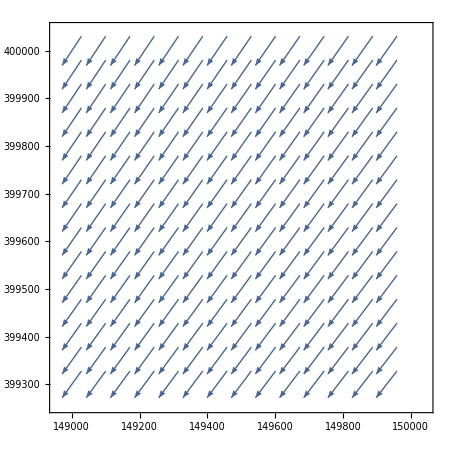

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,149000,150000},{x2,399300,400000}]
(*Near (x1,x2)=(3000,400000)*)
```

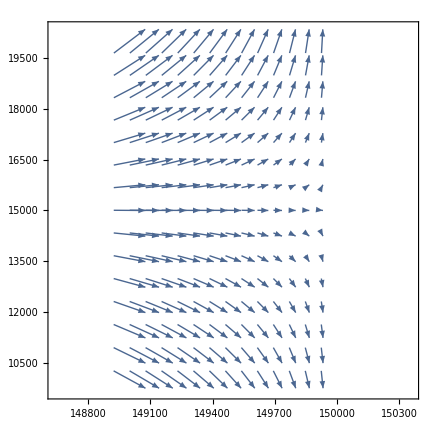

```mathematica
VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,149000,150000},{x2,10000,20000}]
(*Near (x1,x2)=(3000,400000)*)
```

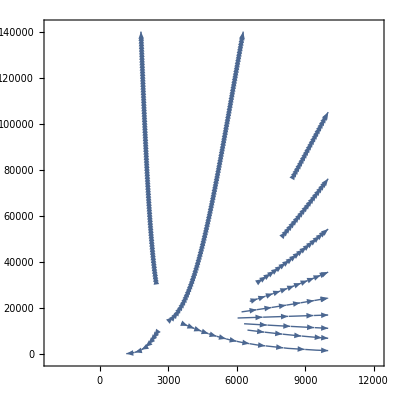

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,10000},{x2,0,140000}]
```

```mathematica
c1=10000
```

10000

```mathematica
StreamPlot[{f1[x1,x2],f2[x1,x2]},{x1,0,150000},{x2,0,400000}]
```

-Graphics-